## Data Exploration

### Wolfram Data Repository

```mathematica
1
```

```mathematica
URLRead["https://datarepository.wolframcloud.com/"]
```

HTTPResponse[…]

### Extracting Data from the Wolfram Data Repository

```mathematica
2
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]
```

ResourceObject[…]

```mathematica
3
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["Properties"]
```

{AllVersions,AutoUpdate,Categories,ContentElementLocations,ContentElements,ContentSize,ContentTypes,ContributorInformation,DefaultContentElement,Description,Details,Documentation,DocumentationLink,DOI,DownloadedVersion,ExampleNotebook,ExampleNotebookObject,Format,InformationElements,Keywords,LatestUpdate,Name,Originator,Properties,ReleaseDate,RepositoryLocation,ResourceLocations,ResourceType,SeeAlso,ShortName,SourceMetadata,UUID,Version,VersionInformation,VersionsAvailable,WolframLanguageVersionRequired}

```mathematica
4
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["ExampleNotebook"]
```

qgekm_shm44FrontEndObject[LinkObject["qgekm_shm", 3, 1]]44Sample-Data-Fishers-Irises_examples.nbCloudObject[https://www.wolframcloud.com/obj/5e59b79e-d95e-4f6f-a7c8-f1276ba17be2]

```mathematica
5
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["ExampleNotebookObject"]
```

CloudObject[https://www.wolframcloud.com/obj/5e59b79e-d95e-4f6f-a7c8-f1276ba17be2]

```mathematica
6
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["Documentation"]
```

URL[https://datarepository.wolframcloud.com/resources/Sample-Data-Fishers-Irises]

```mathematica
7
```

```mathematica
ResourceData[ResourceObject["Sample Data: Fisher's Irises"]]
```

```mathematica
8
```

```mathematica
ResourceObject["Sample Data: Fisher's Irises"]["ContentElements"]
```

{ColumnDescriptions,ColumnTypes,Content,DataType,Dimensions,ObservationCount,RawData,Source,TrainingData,TestData}

```mathematica
9
```

```mathematica
ResourceData[ResourceObject["Sample Data: Fisher's Irises"],"ColumnTypes"]
```

{Numeric,Numeric,Numeric,Numeric,Categorical}

```mathematica
10
```

```mathematica
Column[ResourceData[ResourceObject["Sample Data: Fisher's Irises"],#]&/@{"ColumnDescriptions","Dimensions","Source"}]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}
{150,4}
Fisher,R.A. "The use of multiple measurements in taxonomic problems" Annual Eugenics, 7, Part II, 179-188 (1936); also in "Contributions to Mathematical Statistics" (John Wiley, NY, 1950).

```mathematica
11
```

```mathematica
Fisher=ResourceData[ResourceObject["Sample Data: Fisher's Irises"]];
```

```mathematica
12
```

```mathematica
Fisher[GroupBy["Species"]]
```

```mathematica
13
```

```mathematica
Query[GroupBy[Key["Species"]->KeyTake[{"SepalLength","SepalWidth","PetalLength","PetalWidth"}]]][Fisher]
```

```mathematica
14
```

```mathematica
Query[AssociationThread[Range[Length@#]->Range[Length@#]]][Fisher]&[Fisher]
```

```mathematica
15
```

```mathematica
Fisher[Counts,"Species"]
```

```mathematica
16
```

```mathematica
Query[GroupBy[Key["Species"]->KeyTake[{"SepalLength","SepalWidth","PetalLength","PetalWidth"}]],Mean][Fisher]
```

```mathematica
17
```

```mathematica
Query[Mean][Fisher[[All,2;;5]]]
```

### Descriptive Statistics

```mathematica
18
```

```mathematica
Stats[data_]:=
{
{#[{"Max:",Max@data}]},
{#[{"Min:",Min@data}]},
{#[{"Mean:",Mean@data}]},
{#[{"Median:",Median@data}]},
{#[{"1st quartile:",Quantile[data,0.25]}]},
{#[{"3rd quartile:",Quantile[data,0.75]}]}
}&[Row]
```

```mathematica
19
```

```mathematica
{{#1,#2,#3,#4},{Fisher[Stats,#1],Fisher[Stats,#2],Fisher[Stats,#3],Fisher[Stats,#4]}}&["SepalLength","SepalWidth","PetalLength","PetalWidth"]//Grid
```

SepalLength | SepalWidth | PetalLength | PetalWidth
 |  |  |

```mathematica
20
```

```mathematica
TabView[{#1->Fisher[Stats,#1],#2->Fisher[Stats,#2],#3->Fisher[Stats,#3],#4->Fisher[Stats,#4]},ControlPlacement->Left]&["SepalLength","SepalWidth","PetalLength","PetalWidth"]
```

1234

```mathematica
21
```

```mathematica
Short[Values[Nest[Normal,Fisher,2]]]
{SLall,SWall,PLall,PWall}=%[[All,#]]&/@{2,3,4,5};
```

{{setosa,5.1 cm,3.5 cm,1.4 cm,0.2 cm},{setosa,4.9 cm,3. cm,1.4 cm,0.2 cm},«146»,{virginica,6.2 cm,3.4 cm,5.4 cm,2.3 cm},{virginica,5.9 cm,3. cm,5.1 cm,1.8 cm}}

```mathematica
22
```

```mathematica
{Max[#],Min[#],Median[#],Mean[#],Variance[#],StandardDeviation[#],Skewness[#],Kurtosis[#],Quantile[#,0.25],Quantile[#,.75]}&/@{SLall,SWall,PLall,PWall};
DescriptiveStats=%;
```

```mathematica
23
```

```mathematica
TableHeads={
Style["Sepal Length",#1,ColorData["HTML"]["Maroon"],#2,#3],Style["Sepal Width",#1,ColorData["HTML"]["YellowGreen"],#2,#3],Style["Petal Length",#1,ColorData["HTML"]["SteelBlue"],#2,#3],
Style["Petal Width",#1,ColorData["HTML"]["Orange"],#2,#3]
}&["Title",Italic,20];
TableRows={
Style["Max",#1,#2],Style["Min",#1,#2],Style["Median",#1,#2],Style["Mean",#1,#2],Style["Variance",#1,#2],Style["Standard\n Deviation",#1,#2],Style["Skewness",#1,#2],Style["Kurtosis",#1,#2],Style["1st quartile",#1,#2],Style["3rd quartile",#1,#2]
}&["Text",Italic];
TableForm[DescriptiveStats,TableHeadings->{TableHeads,TableRows}]
```

| Max | Min | Median | Mean | Variance | Standard
 Deviation | Skewness | Kurtosis | 1st quartile | 3rd quartile
Sepal Length | 7.9 cm | 4.3 cm | 5.8 cm | 5.84333 cm | 0.685694 cm^2 | 0.828066 cm | 0.311753 | 2.42643 | 5.1 cm | 6.4 cm
Sepal Width | 4.4 cm | 2. cm | 3. cm | 3.05733 cm | 0.189979 cm^2 | 0.435866 cm | 0.315767 | 3.18098 | 2.8 cm | 3.3 cm
Petal Length | 6.9 cm | 1. cm | 4.35 cm | 3.758 cm | 3.11628 cm^2 | 1.7653 cm | -0.272128 | 1.60446 | 1.6 cm | 5.1 cm
Petal Width | 2.5 cm | 0.1 cm | 1.3 cm | 1.19933 cm | 0.581006 cm^2 | 0.762238 cm | -0.101934 | 1.66393 | 0.3 cm | 1.8 cm

```mathematica
24
```

```mathematica
Transpose[Prepend[DescriptiveStats,TableRows]];
{"   ",Style["Sepal Length",#1,ColorData["HTML"]["Maroon"],#2,#3],Style["Sepal Width",#1,ColorData["HTML"]["YellowGreen"],#2,#3],Style["Petal Length",#1,ColorData["HTML"]["SteelBlue"],#2,#3],
Style["Petal Width",#1,ColorData["HTML"]["Orange"],#2,#3]
}&["Title",Italic,20];
NewTable=Prepend[%%,%];
```

```mathematica
25
```

```mathematica
Grid[NewTable,
ItemSize->{{None, Scaled[0.11], Scaled[0.11],Scaled[0.11]}},Background->{{LightGray},None},Dividers->{{False},{1,2,3,4,5,6,7,8,9,10,11->True,-2->Blue}},Alignment->Center]
```

| Sepal Length | Sepal Width | Petal Length | Petal Width
Max | 7.9 cm | 4.4 cm | 6.9 cm | 2.5 cm
Min | 4.3 cm | 2. cm | 1. cm | 0.1 cm
Median | 5.8 cm | 3. cm | 4.35 cm | 1.3 cm
Mean | 5.84333 cm | 3.05733 cm | 3.758 cm | 1.19933 cm
Variance | 0.685694 cm^2 | 0.189979 cm^2 | 3.11628 cm^2 | 0.581006 cm^2
Standard
 Deviation | 0.828066 cm | 0.435866 cm | 1.7653 cm | 0.762238 cm
Skewness | 0.311753 | 0.315767 | -0.272128 | -0.101934
Kurtosis | 2.42643 | 3.18098 | 1.60446 | 1.66393
1st quartile | 5.1 cm | 2.8 cm | 1.6 cm | 0.3 cm
3rd quartile | 6.4 cm | 3.3 cm | 5.1 cm | 1.8 cm

```mathematica
26
```

```mathematica
Shallow[Values[Nest[Normal,Fisher,2]],1]
```

{«150»}

```mathematica
27
```

```mathematica
Shallow[Cases[%,{"versicolor",__}],1]
{SLVersi,SWVersi,PLVersi,PWVersi}=%[[All,#]]&/@{2,3,4,5};
```

{«50»}

```mathematica
28
```

```mathematica
TableRows;
{Max[#],Min[#],Median[#],Mean[#],Variance[#],StandardDeviation[#],Skewness[#],Kurtosis[#],Quantile[#,0.25],Quantile[#,.75]}&/@{SLVersi,SWVersi,PLVersi,PWVersi};
DescriptiveStats2=Prepend[%,%%];
Transpose[DescriptiveStats2];
{
Style["Versicolor","Text",Red,Italic,20],Style["Sepal Length",#1,ColorData["HTML"]["Maroon"],#2,#3],
Style["Sepal Width",#1,ColorData["HTML"]["YellowGreen"],#2,#3],
Style["Petal Length",#1,ColorData["HTML"]["SteelBlue"],#2,#3],
Style["Petal Width",#1,ColorData["HTML"]["Orange"],#2,#3]
}&["Title",Italic,20];
NewTable2=Prepend[%%,%];
```

```mathematica
29
```

```mathematica
Grid[NewTable2
,ItemSize->{{None, Scaled[0.11], Scaled[0.11],Scaled[0.11]}},Background->{{LightGray},None},Dividers->{{False},{1,2,3,4,5,6,7,8,9,10,11->True,-2->Blue}},Alignment->Center]
```

Versicolor | Sepal Length | Sepal Width | Petal Length | Petal Width
Max | 7. cm | 3.4 cm | 5.1 cm | 1.8 cm
Min | 4.9 cm | 2. cm | 3. cm | 1. cm
Median | 5.9 cm | 2.8 cm | 4.35 cm | 1.3 cm
Mean | 5.936 cm | 2.77 cm | 4.26 cm | 1.326 cm
Variance | 0.266433 cm^2 | 0.0984694 cm^2 | 0.220816 cm^2 | 0.0391061 cm^2
Standard
 Deviation | 0.516171 cm | 0.313798 cm | 0.469911 cm | 0.197753 cm
Skewness | 0.10219 | -0.351867 | -0.588159 | -0.0302363
Kurtosis | 2.40117 | 2.55173 | 2.9256 | 2.51217
1st quartile | 5.6 cm | 2.5 cm | 4. cm | 1.2 cm
3rd quartile | 6.3 cm | 3. cm | 4.6 cm | 1.5 cm

### Dataset Visualization

```mathematica
30
```

```mathematica
Fisher[GroupBy["Species"],DistributionChart[#,PlotTheme->"Classic",PlotLabel->"PetalLength cm",GridLines->Automatic]&,"PetalLength"]
```

```mathematica
31
```

```mathematica
Fisher[GroupBy["Species"],BoxWhiskerChart[#,"Outliers",PlotTheme->"Detailed",ChartLabels->Placed[{"SepalLength cm"},Above],BarOrigin->Right,ChartStyle->Blue]&,"SepalLength"]
```

```mathematica
32
```

```mathematica
Fisher[GroupBy["Species"],Labeled[Histogram[#,ColorFunction->(Hue[3/5,2/3,#]&)],{Rotate["Frequency",90 Degree],"SepalWidth cm"},{Left,Bottom}]&,"SepalWidth"]
```

```mathematica
33
```

```mathematica
Fisher[GroupBy["Species"],Labeled[ListPlot[{#,#}],{Rotate["Sepal width cm",90 Degree],"Sepal length cm"},{Left,Bottom}]&,{"SepalLength","SepalWidth"}]
```

```mathematica
34
```

```mathematica
Short[ResourceData[ResourceObject["Sample Data: Fisher's Irises"],"RawData"]]
```

{«1»}

```mathematica
35
```

```mathematica
Short[Normal[Values[%]]]
```

{{setosa,5.1 cm,3.5 cm,1.4 cm,0.2 cm},{setosa,4.9 cm,3. cm,1.4 cm,0.2 cm},«146»,{virginica,6.2 cm,3.4 cm,5.4 cm,2.3 cm},{virginica,5.9 cm,3. cm,5.1 cm,1.8 cm}}

```mathematica
36
```

```mathematica
Short[Iris=MapAt[QuantityMagnitude,%,{All,2;;5}]]
```

{{setosa,5.1,3.5,1.4,0.2},«148»,{virginica,5.9,3.,5.1,1.8}}

```mathematica
37
```

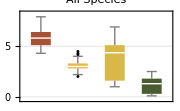
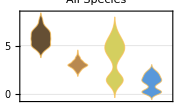

```mathematica
Row[
{
BoxWhiskerChart[{Iris[[All,#1]],Iris[[All,#2]],Iris[[All,#3]],Iris[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"SandyTerrain",PlotLabel->"All Species",GridLines->Automatic,ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],ImageSize->Small],DistributionChart[{Iris[[All,#1]],Iris[[All,#2]],Iris[[All,#3]],Iris[[All,#4]]},PlotRange->Automatic,FrameTicks->True,ChartStyle->"SouthwestColors",PlotLabel->"All Species",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],PlotTheme->"Detailed",GridLines->Automatic,ImageSize->Small]
}]&[2,3,4,5]
```

```mathematica
38
```

```mathematica
Short[Setosa=Cases[Iris,{"setosa",__}]]
Short[Versi=Cases[Iris,{"versicolor",__}]]
Short[Virgin=Cases[Iris,{"virginica",__}]]
```

{{setosa,5.1,3.5,1.4,0.2},«48»,{setosa,5.,3.3,1.4,0.2}}

{{versicolor,7.,3.2,4.7,1.4},«48»,{versicolor,5.7,2.8,4.1,1.3}}

{{virginica,6.3,3.3,6.,2.5},«48»,{virginica,5.9,3.,5.1,1.8}}

```mathematica
39
```

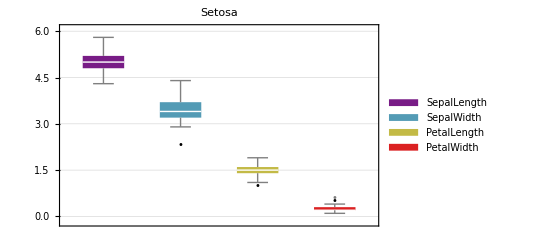
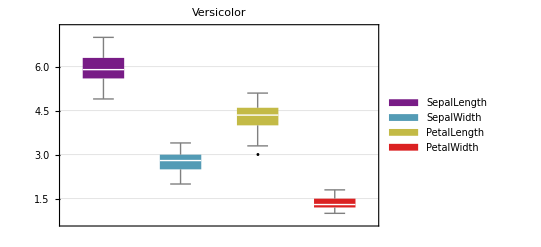
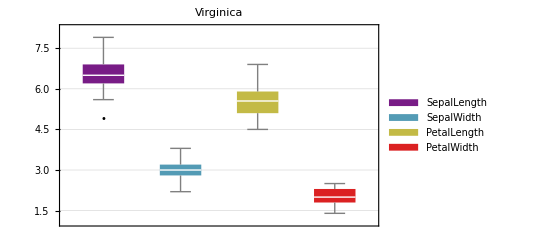

```mathematica
Column@{
BoxWhiskerChart[{Setosa[[All,#1]],Setosa[[All,#2]],Setosa[[All,#3]],Setosa[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"Rainbow",PlotLabel->"Setosa",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],GridLines->Automatic],BoxWhiskerChart[{Versi[[All,#1]],Versi[[All,#2]],Versi[[All,#3]],Versi[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"Rainbow",PlotLabel->"Versicolor",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],GridLines->Automatic],BoxWhiskerChart[{Virgin[[All,#1]],Virgin[[All,#2]],Virgin[[All,#3]],Virgin[[All,#4]]},"Outliers",PlotRange->Automatic,FrameTicks->True,ChartStyle->"Rainbow",PlotLabel->"Virginica",ChartLegends->Placed[{"SepalLength","SepalWidth","PetalLength","PetalWidth"},Bottom],GridLines->Automatic]
}&[2,3,4,5]
```

```mathematica
40
```

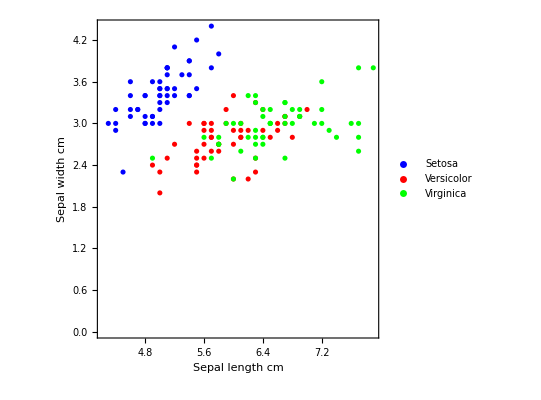

```mathematica
ListPlot[{Setosa[[All,{2,3}]],Versi[[All,{2,3}]],Virgin[[All,{2,3}]]},FrameTicks->All,Frame->True,AspectRatio->1,PlotStyle->{Blue,Red,Green},FrameLabel->{"Sepal length cm","Sepal width cm"},PlotLegends->{"Setosa","Versicolor","Virginica"}]
```

```mathematica
41
```

```mathematica
ListPointPlot3D[{Setosa[[All,{2,3,4}]],Versi[[All,{2,3,4}]],Virgin[[All,{2,3,4}]]},Ticks->All,AspectRatio->1,PlotStyle->{Blue,Red,Green},AxesLabel->{"Sepal length cm","Sepal width cm","Petal Length cm"},PlotLegends->{"Setosa","Versicolor","Virginica"},PlotTheme->"Detailed",ViewPoint->{0, -3, 3}]
```

-Graphics3D-

```mathematica
42
```

```mathematica
Clear[Fisher]
DeleteObject[ResourceObject["Sample Data: Fisher's Irises"]]
```